```mathematica
Forecasting oil prices

The spot prices for Jan 86-Nov 2003:
```

```mathematica
(* data={a,b,c,d,e,f,g,h}; *)
data = {1,2,3,4,5,6,7,8, 1,2,3,4,5,6,7,8}
```

{1,2,3,4,5,6,7,8,1,2,3,4,5,6,7,8}

```mathematica
data
```

{1,2,5,4,5,6,7,8}

```mathematica
data[[4]]
```

4

```mathematica
Length[data]
```

16

```mathematica
swtData = StationaryWaveletTransform[data, DaubechiesWavelet[2], 4]
```

DiscreteWaveletData[«SWT»,<4>,{16}]

```mathematica
swtData["TreeView"]
```

```mathematica
rawSWT = swtData[All] (* Returns Wavelet Coefficients 
						Notice this is an array of lists
						A[[i,1]] returns the "level" (hi/lo)
							i.e. list of 0's and 1's
							0 = lo
						   1 = hi  
						A[[i,2]] returns the coefficients at level i *)
```

{{0}→{5.63397,1.90192,1.63397,3.36603,4.36603,5.36603,6.36603,7.36603,5.63397,1.90192,1.63397,3.36603,4.36603,5.36603,6.36603,7.36603},{1}→{0.732051,2.,-2.73205,-1.11022×10^-16,-2.22045×10^-16,0.,0.,-4.44089×10^-16,0.732051,2.,-2.73205,-1.11022×10^-16,-2.22045×10^-16,0.,0.,-4.44089×10^-16},{0,0}→{6.23205,5.54904,4.5,2.95096,2.76795,3.45096,4.5,6.04904,6.23205,5.54904,4.5,2.95096,2.76795,3.45096,4.5,6.04904},{0,1}→{0.5,0.683013,1.23205,1.91506,0.5,-2.41506,-2.23205,-0.183013,0.5,0.683013,1.23205,1.91506,0.5,-2.41506,-2.23205,-0.183013},{0,0,0}→{4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5},{0,0,1}→{1.73205,1.04904,-2.22045×10^-16,-1.54904,-1.73205,-1.04904,4.44089×10^-16,1.54904,1.73205,1.04904,-2.22045×10^-16,-1.54904,-1.73205,-1.04904,4.44089×10^-16,1.54904},{0,0,0,0}→{4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5},{0,0,0,1}→{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

```mathematica
rawSWT = swtData[Automatic]  (* Returns Wavelet Coefficients *)
```

{{1}→{0.732051,2.,-2.73205,-1.11022×10^-16,-2.22045×10^-16,0.,0.,-4.44089×10^-16,0.732051,2.,-2.73205,-1.11022×10^-16,-2.22045×10^-16,0.,0.,-4.44089×10^-16},{0,1}→{0.5,0.683013,1.23205,1.91506,0.5,-2.41506,-2.23205,-0.183013,0.5,0.683013,1.23205,1.91506,0.5,-2.41506,-2.23205,-0.183013},{0,0,1}→{1.73205,1.04904,-2.22045×10^-16,-1.54904,-1.73205,-1.04904,4.44089×10^-16,1.54904,1.73205,1.04904,-2.22045×10^-16,-1.54904,-1.73205,-1.04904,4.44089×10^-16,1.54904},{0,0,0,1}→{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0,0,0,0}→{4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5}}

```mathematica
rawSWT[[4,2]]
```

{4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5}

```mathematica
Add 0 elements at the begining of list rawSWT[[i,j]] and 1 element to the end.  Determine
the added value by using extroplation with a poly of deg InterpolationOrder
```

```mathematica
extrapolatedData[1] = ArrayPad[rawSWT[[6,2]], {0,1}, "Extrapolated",
InterpolationOrder -> 1]
```

{1.73205,1.04904,-2.22045×10^-16,-1.54904,-1.73205,-1.04904,4.44089×10^-16,1.54904,3.09808}

```mathematica
InverseWaveletTransform[DiscreteWaveletData[rawSWT,DaubechiesWavelet[1]]]
```

{1.,2.,3.,4.,5.,6.,7.,8.}

```mathematica
Last[extrapolatedData[1]]
```

8.36603

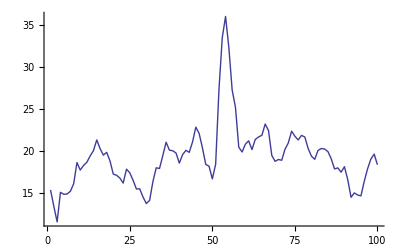

```mathematica
ListPlot[ {spotPrices[[5 ;; 104]]}, Joined -> True, PlotRange -> All ]
```

```mathematica
ListPlot[ smoothData ]
```

ListPlot::lpn: DiscreteWaveletData[«  is not a list of numbers or pairs of numbers.

ListPlot[DiscreteWaveletData[«SWT»,<1>,{215}]]

```mathematica
data1 = {1,2,3,4,5,6,7,8}
```

{1,2,3,4,5,6,7,8}

```mathematica
Length[data1]
```

8

```mathematica
dwt = StationaryWaveletTransform[data1, DaubechiesWavelet[1], 1]
```

DiscreteWaveletData[«SWT»,<1>,{8}]

```mathematica
WaveletListPlot[dwt, PlotLayout -> "CommonYAxis"]
```

-Graphics-